# ON THE SIGN CHANGES OF ψ(x)−x

## Rigorous verification of the computational parts of the proof

M. Grześkowiak, J. Kaczorowski, Ł. Pańkowski, M. Radziejewski

In this notebook we verify Claims 1–5 from Section “The proof of Theorem 1” in our paper “On the sign changes of ψ(x)−x”.

Calculations are based on exact integer and rational numbers and on CenteredInterval objects, through which ARB ball arithmetic is available in Mathematica. The reader may note that the code in this notebook is not based on the code in the other notebook (that describes heuristic computations). Instead we took care to write it from scratch on the basis of the calculations described in the paper. The computation has taken 6 hours (mostly spent on Claim 6) on a MacBook M1 Pro.

By our estimates several GB of free RAM should be sufficient for performing the computation. On our machine the memory used by all variables reported at the end of the computation was 2.25 GB. However, in previous versions of this notebook we noted enormous memory use, in excess of 100 GB. As a result the Mathematica kernel would exit or, on one occasion, the operating system would panic. We could only explain such memory demand by a memory leak bug. The problem no longer seems to occur with the present version of the notebook. In any case, be warned that system instability caused by insufficient memory may have disastrous consequences. If you run the computation on your machine, e.g., to verify our proof, you should use an external monitoring tool to make sure that your system is running with sufficient RAM and in good condition. If you find that there is not the case, quit Mathematica immediately, by whatever (normal or emergency) method your operating system offers. Always keep safe backup copies of important data.

## Initialization

We use rigorous estimates of non-trivial zeros of the Riemann Zeta function from the Flint library that incorporates the ARB library with rigorous ball arithmetic. The imaginary parts of the zeros that we use were obtained by running the example program zeta_zeros.c from the Flint library with the “print_zeros()” function replaced by:

void print_zeros(arb_srcptr p, const fmpz_t n, slong len, slong digits)
{
    slong i;
    fmpz_t k;
    fmpz_init_set(k, n);
    for (i = 0; i < len; i++)
    {
        arb_print(p+i);
        flint_printf("\n");
        fmpz_add_ui(k, k, 1);
    }
    fmpz_clear(k);
}

The program was run as follows :

./zeta_zeros -n 1 -count 22 -digits 1024

to obtain the initial zeros in higher precision and

./zeta_zeros -n 1 -count 10000 -digits 24

to obtain 10000 zeros with about 24 decimal digits precision. The results were copied to the files “zetaZeros22.txt” and “zetaZeros10000.txt”, as arguments to CenteredInterval. These files should be placed in the same directory as the present notebook, so they can be retrieved when evaluating the cell below. We also use two interval representations of π from Flint (with higher and lower precision), obtained with the following code:

void print_pi(slong prec)
{
    arb_t pi; 
    arb_init(pi);
    arb_const_pi(pi, prec);
    arb_print(pi);
    flint_printf("\n");
}

```mathematica
$HistoryLength=0;(*This setting should help reduce memory use.*)
piPrec=CenteredInterval[4990052726770977142154679508178589889026388891990740340505428641215669648447421656627380065252340145932778560702192687029448418415483188954586727357955236838483991113515699969191031129196856848330876927287688269763941393540346541910255624991002971791567097235913963946153048394165591968593437619415761280434402460617709335929051394725822723441471537908256673593130944875014938974955440491292278510804581427338029928540776104319872787747242672692358303125055316299013149608140037453788788861053453199220647499088114236542334675035520389564613678933034002688158602236053046439470764530476520728537596707628174140200257454951588914599592521098835816387920280595104690590499662564424656234943773885248132328562021350799214827268621127807161305325915559963794429078077773411108687974437046305261723935679211260929550307843916995846682043220905771616446457676411836870450668057551979363072001440485851178797768327911193291885089110179181432266964257177844093949635828223079277306912251336430677153648644776417018539522154206415953*2^-3399,536870912*2^-3432];
pi=CenteredInterval[1898976236818169290393997*2^-79,536870912*2^-110];
initialZeros=22;(*Number of initial zeros with higher precision.*)
numZeros=10000;(*Number of zeros computed with lower precision.*)
initialImZero=ReadList[StringJoin[NotebookDirectory[],"zetaZeros22.txt"]];
imZero=ReadList[StringJoin[NotebookDirectory[],"zetaZeros10000.txt"]];
```

## Additional verification of the zeros of ζ(s)

We check that the zeros of ζ(s) obtained from Flint agree with Mathematica’s built-in function ZetaZero[k] and, in the case of the initial 22 zeros, with the estimates published by Andrew Odlyzko.

### Zeros from Mathematica

```mathematica
highPrecision = 1028;
Monitor[initialImZeroMMA=Table[N[Im[ZetaZero[k]],{Infinity,highPrecision}],{k,1,initialZeros}],StringJoin["Computing the initial zeros of ζ(s): ",ToString[k]," of ",ToString[initialZeros]]];
passed=IntervalMemberQ[piPrec,N[Pi,{Infinity,highPrecision}]];
For[k=1,k<=initialZeros,k+=1,
passed=passed&&IntervalMemberQ[initialImZero[[k]],initialImZeroMMA[[k]]]
];
Print["Are the initial 22 zeros (computed with high precision) returned by Mathematica inside the intervals that we use? ", passed];
Parallelize[imZeroMMA=Table[N[Im[ZetaZero[k]],{Infinity,28}],{k,1,numZeros}]];
passed=IntervalMemberQ[pi,N[Pi,{Infinity,26}]];
For[k=1,k<=numZeros,k+=1,
passed=passed&&IntervalMemberQ[imZero[[k]],imZeroMMA[[k]]]
];
Print["Are the initial 10000 zeros returned by Mathematica inside the intervals that we use? ", passed];
```

Are the initial 10000 zeros returned by Mathematica inside the intervals that we use? True

We needed to ask Mathematica to be slightly more precise than Flint, so Mathematica’s result is inside Flint’s interval. Actually, for higher precision and higher zeros we would need even more extra digits, because Mathematica’s built-in ZetaZero[] tends to return results with accuracy slightly below that which is requested. To see this, compare Mathematica’s output to itself, with two different precisions:

```mathematica
N[Im[ZetaZero[9998]],{Infinity,128}]-N[Im[ZetaZero[9998]],{Infinity,140}]
```

-1.600655935553871020306165×10^-103

### Zeros from Odlyzko

Zeros published by Andrew Odlyzko at https://www-users.cse.umn.edu/~odlyzko/zeta_tables/index.html are claimed to be accurate to 1000 decimal digits, but the accuracy is in fact a little higher.

```mathematica
initialImZeroOdl={14.134725141734693790457251983562470270784257115699243175685567460149963429809256764949010393171561012779202971548797436766142691469882254582505363239447137780413381237205970549621955865860200555566725836010773700205410982661507542780517442591306254481978651072304938725629738321577420395215725674809332140034990468034346267314420920377385487141378317356396995365428113079680531491688529067820822980492643386667346233200787587617920056048680543568014444246510655975686659032286865105448594443206240727270320942745222130487487209241238514183514605427901524478338354254533440044879368067616973008190007313938549837362150130451672696838920039176285123212854220523969133425832275335164060169763527563758969537674920336127209259991730427075683087951184453489180086300826483125169112710682910523759617977431815170713545316775495153828937849036474709727019948485532209253574357909226125247736595518016975233461213977316005354125926747455725877801472609830808978600712532087509395997966660675378381214891908864977277554420656532052405,21.022039638771554992628479593896902777334340524902781754629520403587598586068890799713658514180151419533725473642475891383865068603731321262118821624375741669256544711844071194031306725646227792614887337435552059147397132822662470789076753814440726466841906077127569834054514028439923222536788268236111289270057585653273158866604214000907115108009006972002799871101758475196322164968659005748112479386916383518372342780734490239101038504575641215958399921001621834669113158721748057170315793581797724963272407699221125663441561823605180476714422714655559673781247765004555840908644291697757046381655177496445249876742370366456577704837992029270664315837893238009151146858070430828784147861992007607760477484140782738907003895760433245127827863720909303797251823709180804230666738343799022825158287887617612661871382967858745623765006662420780814517636976391374340593412797549697276850306200263121273830462939302565414382374433344022024800453343883072838731260230654753483786801182789317520010690056016544152811050970637593228,25.010857580145688763213790992562821818659549672557996672496542006745092098441644277840238224558062440750471046149055778378299851522730801188133933582671689587225169810438735512928493727191994622975912675478696628856807735070039957723114023284276873669399873219586487752250099192453474976208576612334599735443558367531381265997764529037448496994791137897722066199307189972322549732271630051591619212797740876600067291498308127930667027350849516001984670542469491796695225514179319665391273414521673160233737754489414641711937848957499751411065856287969007670986282721864953729632392584034913871430489335889461149586242390368556175189359878735685683089271444468756375337019130417377142535868018531867896375326868632660719766920532953347850670798287711867494428143972542551653196797799127226844589692794085995072279605136120213696806476533976269691774251249095257214003855886494422730332216278403670865759210329078986615602048427519273514192759701784916608441107482155912831074931422640278339513428773126644105168571016344289902,30.424876125859513210311897530584091320181560023715440180962146036993329389333277920290584293902089110630991711527395499117633226671186319391807225956714243341155906854681365580724173498447249593190408116323150197023484841630221400985620739718392018133021868063298225719752250023746856136974712496442622977924504057490671534572788651506516083246879706281778104577772258789192373862900112760309735680890492530064612892727530919447902003589389819427495511323917384271638108400499211198006924387188729695970002910005477427068908168462593483850770799656037339265916317859005583905968157207307962526205494009595158923181955070031204385472912847073737931700052460469858203860095171051337905912538151203525649548068653947457306442869841989012474276200924947673637581472033220866876014572657774071196727343504792345035161879811455794448693261212914417916583251901867849867644777729648215979712565041026341481014213352401333833266814485615449144877122011828407076516476221131280807023768331017097022722833154052850963731871619582513781,32.935061587739189690662368964074903488812715603517039009280003440784815608630551005938848496135348724549602525280597581513579237782857754506037653011472682109825272713659478166079186507881170353836765474601738548120651787886596466594728787186027971658042677648544066692909393193115645508391751300790279989562656683920024874165169990868845012876404250956064144893023774797053252782409947751765944607446809874067065338290958915614204800224198408375141584435237806584753908207901246070504560100102257438966836495384237704204909559898148908828725637297965721416526317785755201155077784057950147720725798214042130968637793635364185940239585699090026826663214819343540824642411198675065226034566669947805384925779001837592451461820738574360137810637371561037862089022277413320417734643423628639629736284445542467946705724129455369859667727596107799501092598501136571980327345054062391125982107996408750156764769596419463847304800451155728883660650892331803497715016444348320656123479340307063230555187773781024210561808202609296218,37.586178158825671257217763480705332821405597350830793218333001113622149089618537264730329104945823803474577747746192235379940965022263936285624822047483688089003667890354537553777903190905644099375838721275634312643051507490897122077467801551204327992986651432331546548850586795060341362549259966882096153281156037995262203235784878311073776146230149105579379015677163411251265371295650176744886452149832702011984494315326208033153177607464795075040560820830213633950862288220551335769555803593746481598709080074079627217716472274070573805968351484679530321727608711240067379431833670679071307878785388574357730695112597437885627621434891374075997674405555785944574435456054998502810248039697965044333212466041270340603151340824120398066920929558272133080574742240379526941447560387171391417722823862277333504075259600092839740678450396055572399332457099842085439308578390827058000428133328048210695855943079835422972275055349593563168097527417304301276517837886885878256674412456445093066944548079936612500679148846677611635,40.918719012147495187398126914633254395726165962777279536161303667253280528720071282996003719889546875503665519676945467944917136494898599175653436753310504809152168754487522779220070007397194841780564455223010528554611979757902870894436727404629995409604733040969526221562845948429944927846184578787761632678985436277253862556903038183973270514950196665527710349743748816695990528591030482062963647832880205221997318825658012351221409067191689558103853574341088997924759060345757218996039302094745965584290912923566370707188285584612269389815842552303110715447005534211539012118024755248920241853900700081118836575541150867856067645344511425702035874610038012461701591217504665556870944439231103353127472397717165752437859003356150461715730024647846977131484467042381635320368498421857402113983354914271267702876679477362046933993378305961890877026470225234443299092913750722232251216747711999592944915975281247409735591880537231769464032357313745507675771706351076181783304223322787045299728779311668679391883240023041678498,43.327073280914999519496122165406805782645668371836871446878893685521088322305053626456349371063190933554867608492626802447167012325854752123534663067852863346174582283863318197814787695734460590477768591146490300175468026853027496697613091256439069665846196373054906998801694436519162899527326977331224740290290229705567643252015673036580406818855674948098017853704975815364307149372761017706878678433545631903018125851200714770241073205571081343008914241615264552855237368821808322357074175925403682783202820844581402829363318254760866548677482059019431583910734195687649048970000428892587215224344700055116338731895921977292871405903268732616775584130881875117328095378031093324495736965067920017652435206447838972973982815035687933391083370000189268961708105181166948747137174902834881814502124103634888793822523029185271305382416631225364422580899589380998557493636802859408915387487451045248123666445118287217598562223212440326052361942860828927582355882964573021314908449408119052316779053689263761269727183964342502557,48.005150881167159727942472749427516041686844001144425117775312519814090216416308281330335372305400997715502977702602021626521662708135972931666387875848360415749514542594393171912466407742182807931556592203395015105544159539882294586912180255358282132516378822242517229114957339065901571071341609546717615622019577430001371901180892813940745566841311897293679338884843169548510888134892622771079386125445306555452581604302173171394016676219848596815386025310508650393065848664659529280290536587847109504846578979845752160747031322459928624126668913618845629867535245575085897659709700248488816292204313785588540434570627638376649293613060600214542140480454075879271396728375556083478743824757976591799995228735986325938128949255347158323722000074022111362522052401012609727553460151228461942191877772697391549909150902318606173114811362589313765088366719725261497861102030567227613320075475161086258162488087245079880549023530434510965723869519500307655309517952690567582392409346742729337769667984514323479651785659781012585,49.773832477672302181916784678563724057723178299676662100781955750433511611515739278732707507400931330070781628021561131224357999164116355314075451490589915984746411164163782537833166539297285795485833915806394663259736444259036153975727355045500020189054770646843216398460410248730439673334416134296584582373561104085286836170987108253943806072157945484969949480065409184396865322229487965987165345448109651729324403405232091131962150505954273947996858231814508704434773134221635876244264109437986101224081986059357610015828371261358048082733387757025657831644622198428867284811970016458730887608759017366197717169939252440040002704948418830430029679322319955569628185655747157275942398769858510515539714341772965634674500030547079904013941493421313358102814503748399158255171526050338714846544268976795011253932374055783313514741744854577693323020963097267410032271370156512511527718777100048072946537052793939826953074619178922511068291080412495755121845851660686228889552792927764105240258458631087265392319699472946086295,52.970321477714460644147296608880990063825017888821224779900748140317564950304188054137587827094399298803638844775355020280305242142526759718852426729501802899064158884404381357390147898876805601360715184610972725663572678982128874175943840112488882136436086401051818563432220986937961340888420115494236460455276268950852744478613505141202927208507860796499787911644833496246315573764199453751933652840294380978108956576421203896903687370481919718627137671317419749396133269854256578464831198077078267156524968563268104475474900052648115776044246214651286502321748406559148911458922289997095898574003746353078846368818958279125659506201459684206743431171746671164326328999484488107227524047065005394806556803123856288675947364461841065824200330023776589577654842300695926465706803975286536653965330465194390645186172870946450383808883234920314428485578638537642852140837219691328838062211432628271565436562767613276667483291737345439668735430085880540546291402438456489493204139845476289822490179564066261805685631720129786565,56.446247697063394804367759476706127552782264471716631845450969843958475280274505666903011314274852387478971878833682458279533852415440494142677331535851389912303143950977674796418428215141590453279767897067421802190238351965802772317149622477373168417648321033460697211675520831682748713648990126222250598880229523569106175457831955605625499680933974877960385542193898869248985287351051421261197431092358134099013604709239141031109009433319473584228704879584556102786577358526283178106677724885875960578484157909151683055339871132011114436492678493715500047075086672424925572954131702615463031837387640836936950186723039068836450550007327867980999870065617695185049360601192737525309533662000989316467491978423470677395500748300974134269685945837242201426878692945161648904392108877179588832242892099773881781246894312187501531124487772171647170947868970947304805323847847276172776766067483112107631211790935473076225276136187306347951724637196712061707978317457841616417107687158660013365258527155967283425409387438679212449,59.347044002602353079653648674992219031098772806466669698122451754746800152699629811838102487074633548438521958547439243543230918332335569418407300562121738989907621132217768239740056790572042452849526440849681472733038623910280825310642382206849929802500376003172490143770767704346845812728985850745087748420569208096615178589057959523006983053724332333663472331206556204934291015260598686066619048070703221177721893461199933605757933822661462457047598564940384489397956778352154200137916652305382822464848056286397772933081641275862409791391494945884992124254694810686037953826475310083136880636641076605666945474441535613329645619174423369479643126531804294010965039525227559520795006567279336501268658748905330228091635965020782369955967786594161281969630385290278982508036510330745304419563188328073715721694740391394873684888300733513206718053126169663265305833321274938349369740133741459513946477564549783261202953121314681877483549199357103776161517083628727899347884080671159953910723237815412696221153705577228585649,60.831778524609809844259901824524003802910090451219178257101348824808493667294920538430841670394343356569864470335886897450307479486387757151236989677767181392903972554893663963609096708774122166838869036113823238137329669465456300338044996481742040533940870976129782940984400188964842502151111133539340835867006606096578282320208221731557647190053496799727283085923495402643075225018443792153637195364840597773110896607865925425478166991323631938667833621762047903805963775756066867271977573019725620641617070717881201984851940399219428181037789558281013544058327568129857313384547062445399567257041697905384773885295022189922925585387639265939894973177755252302791322676359672466519865985965716901132288333512324701288146549659734648733596733889232923759116870485124568436793317977370468720140175565722622172619376184888086010176402135442138372093901721196117386295372755754110553487919760743047599818014270992473679191478534947036556659099682425949979285417308853699635884621412843441579829363936451921154503226768323665123,65.112544048081606660875054253183705029348149295166722405966501086675343232668685384416774784438659471425896927751662036727792212579760406526710341712839335650466395474113792407738729745594267472413801520291555970661333824803985659298979057804375398625149837486331063458826984693672376060806786223089046279404010250827138638049301763338402226589739859732802755781368511117109763224351292112576574865375509270427021177990914098939023566714960805022355015948341568367529956845298905085088674588430969696692059922085750022986845145268896140456464783480228632260506470176668372559737163741256526487125848152676462750450304365262441290757729753934251933879570045116745923042841923035167267716672756004106536974278267866541063812451435638860089854085737654856110158637493619464000376281191771905035910634753112955650254927935702083940045117469305528656412508982759598261836524699698314147407660309343740846980458044034701255293332123418613818055529567556639834532121517308852126314102010110170914578039124142928133899740086613623443,67.079810529494173714478828896522216770107144951745558874196669551694901218956196983530293975085833034305554701005134859631029151896043171815867354023194548367379040086702914780981794419678446124381438361758449362432396595448051672339388685066004214583341246451635021345298388413847073026983988212589993826423870085245099897564429667355104289878620718854072588546515573973459707071676273108576334932180772579130003960886449741836868715353947764759128350375674332037097265984118710070440446053451664131052421556680265235785072265274438876785626696038697482052096822374418507817943850224433466786174237419767373787309963680688765295690311108804218807366754481244754126423472826840008964978766958987469469952222948151276077984728912688004788165878196172194802776783863053597521117816013422995841342604633581716447324616352745933784570730430336484481280084073724559292321162614130247542832542954781778971577652485927891091400797975856467160901917331051889540357656938483469207036091770874090798196914244237793474312960465161719018,69.546401711173979252926857526554738443012474209602510157324539999663387672274910419533344933178340356353748061584786789166256122868405335227015176432187466163867949293053330205635955993519803439585575951149993338354513925577815476563818784672545960927472810403977949465301956954113198287899441275390567299127186483274427161742404580758998172596532400771329115105700059633507489318776398578809627274125313730703486050666445397940404230923726906435472678042455592779768290482541588859320129640662501737686841432312955689915322050102403360348304793494170171385794877279048931560824211654484121519777177972349155112156370686643979889055753212470390757380586610609056618978691276590975660299730990890514703412420060488566164142937612261486963492359769796863933407019950195728585301788681956625221576313646680279951229456246227494907917846795039656017767699206080410822324119356123825002391567773007065401074770394762661359198236961182883729506234855468174962532618577365999928066108146023977496529241716431832460818788134835630122,72.067157674481907582522107969826168390480906621456697086683306151488407372399608348363525330412174532989157366583118830836423939323964808824558488883908559966767458883026748667191010101895350972098410313771672274863799585130686177614665616376998197197669271905364262584998184369329731220210017215416395486301758548012415863519695592893151923272111791165174080277360316696472824331009518236955764250295787473151203884754319753472903632760869531588040490159640781358830072069132830007220361644959698406819333476590718284182443211058553066580907396128791263351023890940041219029750091157739721366614804245906732824519405223742395049014342105916856145109620394666086341141283207680069777118300539680261625685207183611688073563664855004634873302936891337290063310993337412669550711033660962964462104424684671333751109235686272147335929875463001672771874443478254245459001442104651311737080519674798616116617535063002446065244825392505742634946337840098855132224309529578293821607770227239472724539770409131792951682759339844929414,75.704690699083933168326916762030345922811903530697400301647775301574197027706323608384037021834652798049944023687571004941299377457936923240324919083376086534299429539403011543428535887306752667532417416879534543957049641711755340566565827887197871118390689030240405738091182251987075000006401603759117221197628068776231453643432562273102760140785123571406712732371327300612168974875966764710215388394445911146311030535053974933630568264496513909943445091170178315452780762798464236397482211548344718763384623992318292397085481612509019074177672575428577670559441950731727047461777128106771816527866760625804473224284181811384369765863641702088501826914286557271757830441891394556842493793565722002357598861902102493142375562290110052780709080886377094342840807497709278058388075027628287061481671345250224534613796653218996060425514641725267850975168581757010398813876102074139793312211689814244076676024176863363672137102926551762356450984387409050719186387174232917044907073662920175339770114877282971583201457214164887129,77.144840068874805372682664856304637015796032449234461041765231453151139164253715089408288694699737759759056874412689862739401015043448714791318685067209262509692449500569598542876993525949529386655515907890732199648947712250820352478570207374012914861152103578929079678094268718586402341944783860346706430810880909426809869882058457679190768712226687326836014675913906597219780274184138815734306541730015512005219415994953054177649034287070792970549518522178103669138493110400289908763125838747967104934425409045729053716238542894539734697938404467517845653982842873996850493681944191593492637849172325367363215884466442942711922492108245169377647915815628834469485346686315856231243295323609538238676146113601842703432707855722562393513833974296170905761529531226860673673497802362080120843068941880544294812645599285786304342142860013808561146024088198620632042297490278719397603494739334898514673824383470963996162236863904616161107577611336626543223117952517771125313274971976990352450981517833496024699864255959028093118,79.337375020249367922763592877116228190613246743120030878438720497101541932677090974677451994612124109014771023779750384922652206861281156828604989206199709970777729349241193116002036546210829938880840595591024165836178958610962337370703795074070495164304475690853280666926618655173228169931294828478360202862803490247646424726799729387284332634383628679498838418894491711089737165416455496333704114154400493984706855811753017890603105118296573185573135346696061339024840566012640704135999561500670945543734223534031324396181168051898902903403770497215533001808053796224076169480865529924868274022835773560748385236594010125036441641139088681713752156567009344600198335439524870139087263766766023488607165861620323257974082497049161987413342205324829284332551819386397602705246791700763722091171053670040607336954316681544251161987389754932964386820464175476639079150107912316638712286268910890608385758562065991698091864906907118146357129962123335277141401039892296665852570788470147373858113102405285451703087823709621240231,82.910380854086030183164837494770609497508880593782149146571306283235929086356619075512563192334896818755254481761860100461233852807359574706971433497862880915545409209829902744647007546820535138230602538882436385604843742039067050280111496376921747082104450134056334429211126572475601858904750201748215549748547213195125193479678951287975411253239484602338329388134980206848937216850204264250309056404395393371604415437958809279859505591888303651481971352440868158769637264169441104758931971317075262356082073994618558833265382469388370004986481419937685933144650326403697988041473225617258868002876866036602248640131077429112590790286497528478168503567063434962995385140961764347945100789661299612101531666911126805186624629486792435006021033426362776656461831360740321656215694227198314230318031561342080125413685783092636639888303766029667579048491094809757291004908265664702841020854127757102603929175787723052494939434048863172519380405430299686906077603021369167778237807307169782226106174319793784464130845283261867668};
error=0;
For[k=1,k<=initialZeros,k+=1,
error=Max[error,Abs[Information[initialImZero[[k]],"Center"]-initialImZeroOdl[[k]]]]
];
Print["Maximum difference below : ",Abs[error]<10^(-1022)];
```

Maximum difference below : True

## Claim 1

We have  and  for .

As a rule, we try to represent all the data as it appears in the paper. Unfortunately, we are forced by Mathematica to use 1-based array indexing. For  and  we use functions to simulate 0-based arrays, but for the arrays z1 and alpha we need to remember that indices are off by 1. As Mathematica reserves all names starting with capital letters, objects named with capital letters in the paper are preceded with c, e.g., cN for “capital N”.

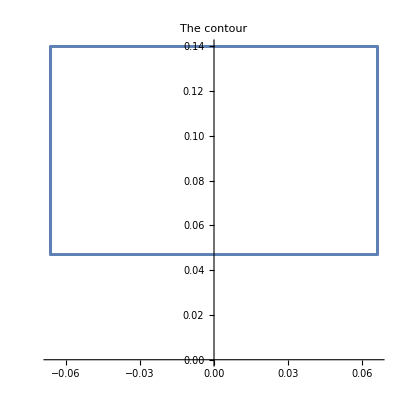

Claim 1: True

```mathematica
cN=21;
gamma[n_]:=imZero[[n+1]];
rho[n_]:=1/2+I*gamma[n];
omega[n_]:=gamma[n]-gamma[0];
cFNeta[z_]:=1-Sum[Abs[rho[0]/rho[n]]Exp[I omega[n]z],{n,1,cN}];
f[z_]:=-Sum[I omega[n] Abs[rho[0]/rho[n]]Exp[I omega[n]z],{n,1,cN}];
delta=132737/10^6;
y0=468918/10^7;
y1=14/100;
m=12000;
z1=Join[
Table[4 t delta+y0 I,{t,0,1/8,1/m}],
Table[delta/2+(y0+4(t-1/8)(y1-y0)) I,{t,1/8+1/m,3/8,1/m}],
Table[-4(t-1/2)delta+y1 I,{t,3/8+1/m,5/8,1/m}],
Table[-delta/2+(y1+4(t-5/8)(y0-y1)) I,{t,5/8+1/m,7/8,1/m}],
Table[4(t-1)delta+y0 I,{t,7/8+1/m,1,1/m}]
]; (* i.e. z1[[1]],...,z[[m+1]] represent .
*)
(* The argument function, denoted as  in the paper, is called argFun[t] here. *)
argFunBreakpoints={0,1/32,1/8,3/16,3/8,1/2};
argFunValues={0,489819/10^6,185802/10^5,204829/10^5,290189/10^5,pi};
argFun[t_]:=Simplify[Piecewise[Table[{(argFunValues[[j]]*(argFunBreakpoints[[j+1]]-t)+argFunValues[[j+1]]*(t-argFunBreakpoints[[j]]))/(argFunBreakpoints[[j+1]]-argFunBreakpoints[[j]]),argFunBreakpoints[[j]]<=t<=argFunBreakpoints[[j+1]]},{j,5}]]];
alpha=Join[
Table[-pi+argFun[(j-1/2)/m],{j,1,m/2}],
Table[pi - argFun[(m+1/2-j)/m],{j,m/2+1,m}]
];
alpha=Join[{alpha[[m]]-2pi},alpha,{2pi+alpha[[1]]}]; (* i.e. alpha[[j+1]] represents  in the paper. *)
Print[ComplexListPlot[z1,AspectRatio->1,PlotLabel->"The contour "]];Print["Claim 1: ",Max[Table[Abs[alpha[[j+1]]-alpha[[j]]],{j,1,m}]]<pi&&Max[Table[Abs[z1[[j+1]]-z1[[j]]],{j,1,m}]]<pi/omega[cN]];
```

## Claim 2

We have  for .

```mathematica
b=Table[(1/2)Abs[z1[[j]]-z1[[j+1]]],{j,1,m}];
xPrime=Table[Min[Re[z1[[j]]],Re[z1[[j+1]]]],{j,1,m}]; (*  *)
xBis=Table[Max[Re[z1[[j]]],Re[z1[[j+1]]]],{j,1,m}]; (*  — we use the Latin "bis" instead of "double prime" *)
y=Table[Min[Im[z1[[j]]],Im[z1[[j+1]]]],{j,1,m}];
cM=Table[Sum[Abs[rho[0]/rho[n]]omega[n]^2Exp[-omega[n]y[[j]]],{n,1,cN}],{j,1,m}];
cNPrime=9998;
cT1=(gamma[cNPrime]+gamma[cNPrime+1])/2;
cRN[y_]:=Sum[Abs[rho[0]/rho[n]]Exp[-omega[n]y],{n,cN+1,cNPrime}]+Exp[(gamma[0]-cT1)y]*(Abs[rho[0]]/cT1)(Log[cT1]/(2 pi y)+4 Log[cT1]+2/(cT1 y));
yUnique=Union[y];
Monitor[cRNLookup=Association[Table[yUnique[[j]]->cRN[yUnique[[j]]],{j,1,Length[yUnique]}]],
StringJoin["Precomputing : ",ToString[j]," of ",ToString[Length[yUnique]],"."]];
Monitor[u=Table[Min[
Re[cFNeta[z1[[j]]]Exp[-I alpha[[j+1]]]]+Min[0,Re[b[[j]]f[z1[[j]]]Exp[-I alpha[[j+1]]]]],
Re[cFNeta[z1[[j+1]]]Exp[-I alpha[[j+1]]]]+Min[0,-Re[b[[j]]f[z1[[j+1]]]Exp[-I alpha[[j+1]]]]]
]-b[[j]]^2cM[[j]]/2-cRNLookup[y[[j]]],
{j,1,m}],
StringJoin["Computing : ",ToString[j]," of ",ToString[m],"."]];
Print["Claim 2: ",Min[u]>0];
```

Claim 2: True

## Claim 3

We have  for  and .

```mathematica
(*We have to define our own rigorous floor and ceiling functions,as Mathematica does not seem to support Floor[CenteredInterval[...]].*)
floor[ball_]:=Module[
{x=Information[ball,"Center"],n},
n=Floor[x];
If[n<=ball,
Return[n]
];
Print["Indeterminate floor of ",ball,"."];
Return[Floor[ball]]
];
ceiling[ball_]:=Module[
{x=Information[ball,"Center"],n},
n=Ceiling[x];
If[n>=ball,
Return[n]
];
Print["Indeterminate ceiling of ",ball,"."];
Return[Ceiling[ball]]
];
norm[ball_]:=Min[ball-floor[ball],ceiling[ball]-ball];
Module[{var=""},
Monitor[
var="";
betaPrime=Table[Table[
pi+omega[n]xPrime[[j]]-alpha[[j+1]],
{j,1,m}],{n,1,cN}];
var="";
betaBis=Table[Table[
pi+omega[n]xBis[[j]]-alpha[[j+1]],
{j,1,m}],{n,1,cN}];
var="";
phiPrime=Table[Table[
Piecewise[{
{0,ceiling[betaPrime[[n]][[j]]/(2pi)]<=floor[betaBis[[n]][[j]]/(2pi)]},
{2pi Min[norm[betaPrime[[n]][[j]]/(2pi)],norm[betaBis[[n]][[j]]/(2pi)]],ceiling[1/2+betaPrime[[n]][[j]]/(2pi)]<=floor[1/2+betaBis[[n]][[j]]/(2pi)]}
},
2pi Min[norm[betaPrime[[n]][[j]]/(2pi)],norm[betaBis[[n]][[j]]/(2pi)]]
],
{j,1,m}],{n,1,cN}];
var="";
phiBis=Table[Table[
Piecewise[{
{2pi Max[norm[betaPrime[[n]][[j]]/(2pi)],norm[betaBis[[n]][[j]]/(2pi)]],ceiling[betaPrime[[n]][[j]]/(2pi)]<=floor[betaBis[[n]][[j]]/(2pi)]},
{pi,ceiling[1/2+betaPrime[[n]][[j]]/(2pi)]<=floor[1/2+betaBis[[n]][[j]]/(2pi)]}
},
2pi Max[norm[betaPrime[[n]][[j]]/(2pi)],norm[betaBis[[n]][[j]]/(2pi)]]
],
{j,1,m}],{n,1,cN}];
,
StringJoin["Computing ",var," for n = ",ToString[n],"."]];
];
Print["Claim 3: ",Max[Table[Table[betaBis[[n]][[j]]-betaPrime[[n]][[j]],{j,1,m}],{n,1,cN}]]<pi];
```

Claim 3: True

## Claim 4

There exists a matrix  with integer coefficients such that  for .

We perform an adapted LLL algorithm, described as Algorithm 1 in the paper. Some of the notation is as in Algorithm 1 and Proposition 2. We write inputU for , vec for , coeffsBound for  and coeffs for  here, because the names u, v, M and c also appear in the main part of the proof of Theorem 1. First we use standard Mathematica high-precision numbers to perform the algorithm (find the coefficients). Then rigorous intervals are used to verify the claim.

```mathematica
theta=Table[(initialImZeroMMA[[n+1]]-initialImZeroMMA[[1]])/(2 π),{n,1,cN}];
e=Table[Table[If[k==n,1,0],{k,1,cN}],{n,1,cN}];
inputU=Table[e[[n]]-theta*((e[[n]].theta)/(theta.theta)),{n,1,cN}];
δ=1/4;
coeffsBound=10^300;
vec=inputU;
coeffs=Table[Table[If[k==l,1,0],{k,1,cN}],{l,1,cN}];
mu=Table[Table[0,{k,1,l-1}],{l,1,cN}];(*This is just to set up the table structure.*)
vStar=vec;(*To set up the table structure.*)
cB=Table[0,{k,1,cN}];
update[l_,m_]:=
Module[{i,j},
For[i=1,i<l,i++,
For[j=l,j<=m,j++,
mu[[j]][[i]]=(vec[[j]].vStar[[i]])/cB[[i]]
]
];
For[i=l,i<=cN,i++,
vStar[[i]]=vec[[i]]-Sum[mu[[i]][[j]]*vStar[[j]],{j,1,i-1}];
cB[[i]]=vStar[[i]].vStar[[i]];
For[j=i+1,j<=cN,j++,
mu[[j]][[i]]=(vec[[j]].vStar[[i]])/cB[[i]]
]
];
];
update[1,cN];
k=2;
Until[k==cN+1,
For[j=k-1,j>=1,j--,
q=Round[mu[[k]][[j]]];
If[Max[Abs[coeffs[[k]]-q coeffs[[j]]]]>coeffsBound,
Return[]
];
coeffs[[k]]-=q coeffs[[j]];
vec[[k]]=Sum[coeffs[[k]][[j]]*inputU[[j]],{j,1,cN}];
update[k,k]
];
If [cB[[k]]>=(δ-mu[[k]][[k-1]]^2)cB[[k-1]],
k+=1
,
{coeffs[[k-1]],coeffs[[k]]}={coeffs[[k]],coeffs[[k-1]]};
{vec[[k-1]],vec[[k]]}={vec[[k]],vec[[k-1]]};
update[k-1,k];
k=Max[2,k-1]
]
];
d=Sum[Abs[vec[[k]]],{k,1,cN}];
Print[" estimate: ",N[Max[d],10]];
thetaBalls=Table[(initialImZero[[n+1]]-initialImZero[[1]])/(2 piPrec),{n,1,cN}];
inputUBalls=Table[e[[n]]-thetaBalls*((e[[n]].thetaBalls)/(thetaBalls.thetaBalls)),{n,1,cN}];
vecBalls=Table[Sum[coeffs[[k]][[j]]*inputUBalls[[j]],{j,1,cN}],{k,1,cN}];
Print["Claim 4: ",Max[Sum[Abs[vecBalls[[k]]],{k,1,cN}]]<166*10^(-15)];
```

estimate: 1.655336986×10^-13

Claim 4: True

## Claim 5

Claim 5 in the paper comprises the preliminary part “There exist  satisfying  and  for ”, and the final estimate:

The pre-computed values of , of which we claim that they exist, are supplied in external files:

x1.txt, ..., x21.txt

that should be placed in the same directory as the present notebook (and should be available from the same source as this notebook). If they are unavailable (or in the wrong directory), you should receive an error message. If the file contents is incorrect, the behaviour is hard to predict — Mathematica may run for hours processing the input that it did not understand (keeping it in symbolic form).

The reader need not recreate those files to verify the proof. It is quite sufficient to check that the values supplied in our files satisfy the claims.

```mathematica
l=16000;(*The resolution for approximating the weights or penalty functions.*)
SetOptions[$FrontEndSession,DynamicEvaluationTimeout->Infinity];
v[ϕ_,ψ_]:=Piecewise[{{Cos[ϕ]-Cos[ϕ+ψ],ϕ+ψ<=pi}},Cos[ϕ]+1];
epsilon=2*166*10^(-15);
verifyFormat[x_]:=
Module[{k},
If[
Length[x]==l,
For[k=1,k<=l,k+=1,
If[Head[x[[k]]]!=Rational,
Return[False]
]
];
True,
False
]
];
passed=True;
For[n=1,n<=cN,n+=1,
memu=MemoryInUse[];
c=Table[
Abs[rho[0]/rho[n]]/(u[[j]]Exp[omega[n]y[[j]]]
Piecewise[{
{Cos[phiBis[[n]][[j]]/2-phiPrime[[n]][[j]]/2],phiBis[[n]][[j]]<=pi/2},
{1,phiPrime[[n]][[j]]>=pi/2}
},Cos[pi/4-phiPrime[[n]][[j]]/2]
]),
{j,1,m}];
c=Join[{Max[Table[
(Abs[rho[0]/rho[n]]/(u[[j]]Exp[omega[n]y[[j]]]))
Piecewise[{
{0,phiBis[[n]][[j]]<pi/2},
{0,phiPrime[[n]][[j]]>pi/2}
},1/Cos[pi/4-phiPrime[[n]][[j]]/2]
],
{j,1,m}]]},c,c];
phi=Join[{pi/2},phiPrime[[n]],phiBis[[n]]];
x=ReadList[StringJoin[NotebookDirectory[],"x",ToString[n],".txt"]];
If[verifyFormat[x],
diff=Table[Piecewise[
{{x[[k]]-x[[k-1]],k≠1}},
x[[1]]
],{k,1,l}];(*The list of lists of differences .*)
passed=passed&&(Min[diff]>=0&&Max[x]<=1/2-epsilon);
Monitor[
For[j=1,j<=Length[c],j+=1,
maxk=Min[l,ceiling[l c[[j]](Cos[phi[[j]]]+1)]];
For[k=1,k<=maxk,k+=1,
passed=passed&&(c[[j]]v[phi[[j]],2pi (epsilon+x[[k]])]<=k/l);
];
];
,
Column[{StringJoin["Checking  for n = ",ToString[n],", j = ",ToString[j]," of ",ToString[Length[c]],"."],StringJoin["Memory in use: ",ToString[N[MemoryInUse[]/2^30,{Infinity,3}]], " GB by all data in the current session, ",ToString[N[(Max[0,MemoryInUse[]-memu])/2^30,3]], " GB by the check for the current n."]}]];
,
Print["Problem reading the file ",StringJoin[NotebookDirectory[],"x",ToString[n],".txt"]];
];
Clear[c,phi,x];
];
Print["Claim 5, preliminary checks: ",passed];
diff=Table[{},{n,1,cN}];(*The variable to store the differences .*)
For[n=1,n<=cN,n+=1,
x=ReadList[StringJoin[NotebookDirectory[],"x",ToString[n],".txt"]];
If[verifyFormat[x],
diff[[n]]=Table[Piecewise[
{{x[[k]]-x[[k-1]],k≠1}},
x[[1]]
],{k,1,l}];
,
Print["Problem reading the file ",StringJoin[NotebookDirectory[],"x",ToString[n],".txt"]];
Break[];
];
];
If[n>cN,last=diff[[cN]];
For[n=cN-1,n>=1,n-=1,
Print["The computation of  for n = ",n," started with ",N[MemoryInUse[]/2^30,{Infinity,3}], " GB of memory in use."];
Parallelize[conv=Table[Sum[diff[[n]][[i]]last[[k-i]],{i,1,k-1}],{k,1,l}]];
last=conv;
];
final=(2/delta)2^cN Sum[last[[k]],{k,1,l}];
Print["Claim 5, final estimate: ",N[final,5]];
Print["Claim 5, final estimate > 1/60: ",final>1/60];
];
StringJoin["Memory in use at the end of the computation: ",ToString[N[MemoryInUse[]/2^30,{Infinity,3}]], " GB."]
```

Claim 5, preliminary checks: True

The computation of  for n = 20 started with 2.22 GB of memory in use.

The computation of  for n = 19 started with 2.22 GB of memory in use.

The computation of  for n = 18 started with 2.22 GB of memory in use.

The computation of  for n = 17 started with 2.22 GB of memory in use.

The computation of  for n = 16 started with 2.22 GB of memory in use.

The computation of  for n = 15 started with 2.22 GB of memory in use.

The computation of  for n = 14 started with 2.22 GB of memory in use.

The computation of  for n = 13 started with 2.22 GB of memory in use.

The computation of  for n = 12 started with 2.22 GB of memory in use.

The computation of  for n = 11 started with 2.23 GB of memory in use.

The computation of  for n = 10 started with 2.23 GB of memory in use.

The computation of  for n = 9 started with 2.23 GB of memory in use.

The computation of  for n = 8 started with 2.23 GB of memory in use.

The computation of  for n = 7 started with 2.23 GB of memory in use.

The computation of  for n = 6 started with 2.24 GB of memory in use.

The computation of  for n = 5 started with 2.24 GB of memory in use.

The computation of  for n = 4 started with 2.24 GB of memory in use.

The computation of  for n = 3 started with 2.24 GB of memory in use.

The computation of  for n = 2 started with 2.24 GB of memory in use.

The computation of  for n = 1 started with 2.25 GB of memory in use.

Claim 5, final estimate: 0.016676

Claim 5, final estimate > 1/60: True

Memory in use at the end of the computation: 2.25 GB.

## Computation of (optional, overwrites files)

This subsection is here only for information on how we obtained the precomputed values of . It is not necessary to re-evaluate it even if you wish to confirm the validity of the proof. If you do run it, you will be overwriting files named

x1.txt, ..., x21.txt

in the directory containing the present notebook. We advise against it, as any malfunction, bug, or mistake, may result in data loss. Accordingly, all the code in this section was commented out. If you do run it, keep an eye on the memory availability (see the introductory part of this notebook), as we did observe excessive memory use when evaluating the xCompute[] function.

```mathematica
(*xCompute[n_]:=Module[{t=AbsoluteTime[],memu=MemoryInUse[],var,c,phi,x,maxk,j,k},
Monitor[
var="";
c=Table[
Abs[rho[0]/rho[n]]/(u[[j]]Exp[omega[n]y[[j]]]
Piecewise[{
{Cos[phiBis[[n]][[j]]/2-phiPrime[[n]][[j]]/2],phiBis[[n]][[j]]<=pi/2},
{1,phiPrime[[n]][[j]]>=pi/2}
},Cos[pi/4-phiPrime[[n]][[j]]/2]
]),
{j,1,m}];
var="";
c=Join[{Max[Table[
(Abs[rho[0]/rho[n]]/(u[[j]]Exp[omega[n]y[[j]]]))
Piecewise[{
{0,phiBis[[n]][[j]]<pi/2},
{0,phiPrime[[n]][[j]]>pi/2}
},1/Cos[pi/4-phiPrime[[n]][[j]]/2]
],
{j,1,m}]]},c,c];
,
StringJoin["Computing ",var," for n = ",ToString[n],", j = ",ToString[j],"."]
];
phi=Join[{pi/2},phiPrime[[n]],phiBis[[n]]];
Monitor[
var="";
x=Table[1/2-(3/2)epsilon,{k,1,l}];
For[j=1,j<=Length[c],j+=1,
maxk=Min[l,ceiling[l c[[j]](Cos[phi[[j]]]+1)]];
For[k=1,k<=maxk,k+=1,
If[c[[j]](1+Cos[phi[[j]]])>k/l,
x[[k]]=Min[x[[k]],Information[(ArcCos[Cos[phi[[j]]]-k/(l c[[j]])]-phi[[j]])/(2 pi),"Bounds"][[1]]-(3/2)epsilon];
]
];
];
,
Column[{StringJoin["Computing ",var," for n = ",ToString[n],", j = ",ToString[j]," of ",ToString[Length[c]],"."],StringJoin["Memory in use: ",ToString[N[MemoryInUse[]/2^30,{Infinity,3}]], " GB by all data in the current session, ",ToString[N[(MemoryInUse[]-memu)/2^30,{Infinity,3}]], " GB by the computation for the current n."]}]];
Export[StringJoin[NotebookDirectory[],"x",ToString[n],".txt"],x];
If[x==ReadList[StringJoin[NotebookDirectory[],"x",ToString[n],".txt"]],
Print["The values of  for n=",n," were saved to the file x",n,".txt in the notebook's directory."];,
Print["The values of  for n=",n," were saved to the file x",n,".txt, but could not be read back correctly."];
];
Clear[c,phi,x];
Print["This computation (for n=",n,") has taken ",Ceiling[(AbsoluteTime[]-t)/60]," minute(s) and increased the memory in use by about ",N[(MemoryInUse[]-memu)/2^30,3]," GB"];
];*)
```

```mathematica
(*xCompute[1];*)
```

The values of  for n=1 were saved to the file x1.txt in the notebook's directory.

This computation (for n=1) has taken 64 minute(s) and increased the memory in use by about 2.15 GB

```mathematica
(*xCompute[2];*)
```

The values of  for n=2 were saved to the file x2.txt in the notebook's directory.

This computation (for n=2) has taken 62 minute(s) and increased the memory in use by about 1.73 GB

```mathematica
(*xCompute[3];*)
```

The values of  for n=3 were saved to the file x3.txt in the notebook's directory.

This computation (for n=3) has taken 35 minute(s) and increased the memory in use by about 1.15 GB

```mathematica
(*xCompute[4];*)
```

The values of  for n=4 were saved to the file x4.txt in the notebook's directory.

This computation (for n=4) has taken 29 minute(s) and increased the memory in use by about 0.97 GB

```mathematica
(*xCompute[5];*)
```

The values of  for n=5 were saved to the file x5.txt in the notebook's directory.

This computation (for n=5) has taken 21 minute(s) and increased the memory in use by about 0.726 GB

```mathematica
(*xCompute[6];*)
```

The values of  for n=6 were saved to the file x6.txt in the notebook's directory.

This computation (for n=6) has taken 16 minute(s) and increased the memory in use by about 0.569 GB

```mathematica
(*xCompute[7];*)
```

The values of  for n=7 were saved to the file x7.txt in the notebook's directory.

This computation (for n=7) has taken 13 minute(s) and increased the memory in use by about 0.46 GB

```mathematica
(*xCompute[8];*)
```

The values of  for n=8 were saved to the file x8.txt in the notebook's directory.

This computation (for n=8) has taken 9 minute(s) and increased the memory in use by about 0.324 GB

```mathematica
(*xCompute[9];*)
```

The values of  for n=9 were saved to the file x9.txt in the notebook's directory.

This computation (for n=9) has taken 8 minute(s) and increased the memory in use by about 0.253 GB

```mathematica
(*xCompute[10];*)
```

The values of  for n=10 were saved to the file x10.txt in the notebook's directory.

This computation (for n=10) has taken 6 minute(s) and increased the memory in use by about 0.193 GB

```mathematica
(*xCompute[11];*)
```

The values of  for n=11 were saved to the file x11.txt in the notebook's directory.

This computation (for n=11) has taken 5 minute(s) and increased the memory in use by about 0.143 GB

```mathematica
(*xCompute[12];*)
```

The values of  for n=12 were saved to the file x12.txt in the notebook's directory.

This computation (for n=12) has taken 4 minute(s) and increased the memory in use by about 0.111 GB

```mathematica
(*xCompute[13];*)
```

The values of  for n=13 were saved to the file x13.txt in the notebook's directory.

This computation (for n=13) has taken 3 minute(s) and increased the memory in use by about 0.0974 GB

```mathematica
(*xCompute[14];*)
```

The values of  for n=14 were saved to the file x14.txt in the notebook's directory.

This computation (for n=14) has taken 2 minute(s) and increased the memory in use by about 0.0666 GB

```mathematica
(*xCompute[15];*)
```

The values of  for n=15 were saved to the file x15.txt in the notebook's directory.

This computation (for n=15) has taken 2 minute(s) and increased the memory in use by about 0.0558 GB

```mathematica
(*xCompute[16];*)
```

The values of  for n=16 were saved to the file x16.txt in the notebook's directory.

This computation (for n=16) has taken 2 minute(s) and increased the memory in use by about 0.0448 GB

```mathematica
(*xCompute[17];*)
```

The values of  for n=17 were saved to the file x17.txt in the notebook's directory.

This computation (for n=17) has taken 2 minute(s) and increased the memory in use by about 0.0357 GB

```mathematica
(*xCompute[18];*)
```

The values of  for n=18 were saved to the file x18.txt in the notebook's directory.

This computation (for n=18) has taken 1 minute(s) and increased the memory in use by about 0.0259 GB

```mathematica
(*xCompute[19];*)
```

The values of  for n=19 were saved to the file x19.txt in the notebook's directory.

This computation (for n=19) has taken 1 minute(s) and increased the memory in use by about 0.0229 GB

```mathematica
(*xCompute[20];*)
```

The values of  for n=20 were saved to the file x20.txt in the notebook's directory.

This computation (for n=20) has taken 1 minute(s) and increased the memory in use by about 0.0189 GB

```mathematica
(*xCompute[21];*)
```

The values of  for n=21 were saved to the file x21.txt in the notebook's directory.

This computation (for n=21) has taken 1 minute(s) and increased the memory in use by about 0.0141 GB